## Boundary-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 11:22:05
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (2.3.5 (6-Nov-2012)) loaded Thu 8 Nov 2012 18:30:27
using xCellerator 0.90 and XSSA 1204002

```mathematica
poly={{0,0}, {1,0}, {5,1}, {1, 3}};
```

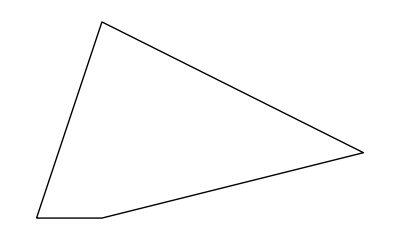

```mathematica
Boundary[poly]
```

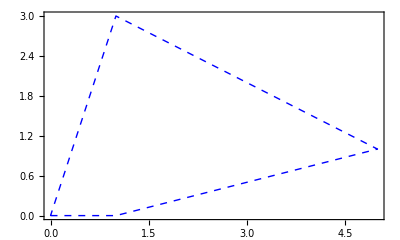

```mathematica
Show[Boundary[poly, {Blue, Dashed, Thick}], Frame-> True]
```

## Demonstrate the problem with Line

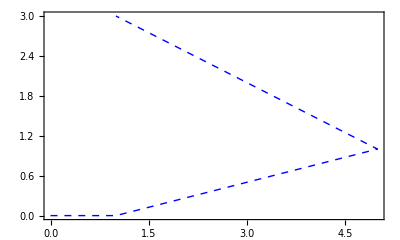

```mathematica
Show[Graphics[{Blue, Dashed, Thick, Line[poly]}], Frame-> True]
```